# Tight-binding Band Structures

## Marvin Poul, University of Stuttgart

## Motivation

```mathematica
DOS1D[Disp_, n_ : 1000] := Histogram[Flatten @ Table[Disp , {k, -π, π, 2π/n}], n/10, "PDF",
PlotLabel -> "1D DOS"];

Manipulate[With[
{disp = (t0 + 2t1 Cos[k] + 2t2 Cos[2k] + 2t3 Cos[3k]) / (1 + 2s1  Cos[k] + 2s2 Cos[2k] + 2s3 Cos[3k])},
GraphicsRow[{
Plot[ disp,
	{k, -π, π}, PlotLabel -> "1D Tight Binding", AxesLabel -> {k, "E(k)"}],
DOS1D[disp, 5000]}]],
{t0, 0, 2}, {t1, 0, -1}, {{t2, 0}, -1, 1}, {{t3, 0}, -1, 1},
{s1, 0, .5}, {s2, 0, .5}, {s3, 0, .5}]
```

## Single Bands

Dispersion is given by E(k) = H(k)/S(k) or

E(k) = E_(0 +)((t_0+∑)_(n=1)^N ⅇ^ikR_n H_n)/(1 + ∑_(n=1)^N ⅇ^ikR_n S_n)

Square unit cell, one atom with one orbital per unit cell, nearest neighbour only

```mathematica
PlotDispersion2D[Disp_, OptionsPattern[{Levels -> 5, Title -> None}]] :=
Plot3D[Disp, {Subscript[k, x], -π, π}, {Subscript[k, y], -π, π}, MeshFunctions-> {#3 &}, ColorFunction-> "BlueGreenYellow",
   			AxesLabel -> {Subscript[k, x], Subscript[k, y], "E(k)"},
			PlotLabel -> OptionValue["Title"], PlotLegends -> Automatic, Mesh -> OptionValue["Levels"]]
PlotDispersion2DContour[Disp_, OptionsPattern[{Levels -> 5, Title -> None}]] :=
ContourPlot[Disp, {Subscript[k, x], -π, π}, {Subscript[k, y], -π, π}, ColorFunction-> "BlueGreenYellow",
			FrameLabel -> {Subscript[k, x], Subscript[k, y]}, Ticks -> Table[Table[{π*i/2, π*i/2/a}, {i, -2, 2}], 2],
			PlotLabel -> OptionValue["Title"], PlotLegends -> Automatic, Contours -> OptionValue["Levels"]];
ConvertDirection[Dir_] := If[IntegerQ[Dir],
IntegerDigits[Dir, 10, 2],
Dir];
Cosine2D[E_, basis_, kMap_] := E + Plus @@
KeyValueMap[∑_(i = 1)^Length[#2] 2  #2⟦i⟧Cos[i*(basis . ConvertDirection[#1]) . {Subscript[k, x], Subscript[k, y]}] &] @ kMap;
Full2D[E_, basis_, Hopping_, Overlap_ : <||>] := Cosine2D[E, basis, Hopping] / Cosine2D[1, basis, Overlap];
```

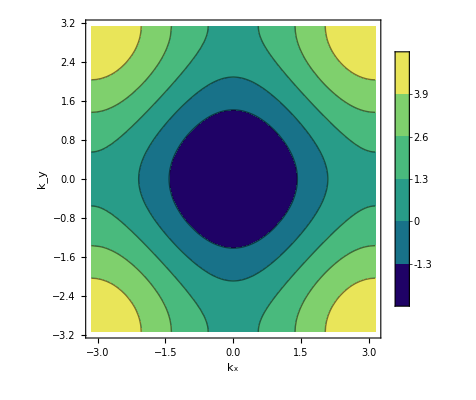
Basis:  | (1. | 0.
0. | 1.)
Hopping:  | {-1.}
Dispersion:  | 1.-2. Cos[0.+1. k_x]-2. Cos[0.+1. k_y]
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 0.}, {0., 1.}};
orbitalEnergy = 1.;
hop = {-1.};
band := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop |>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

Oblique unit cell, one atom with one orbital per unit cell, nearest neighbour only

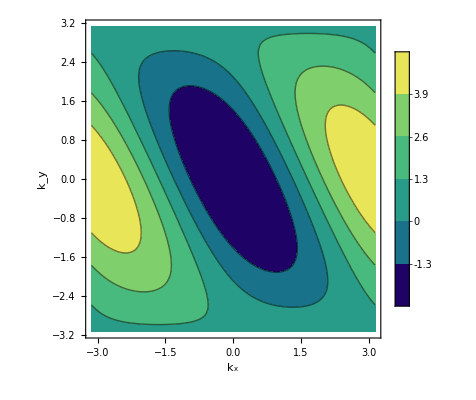
Basis:  | (1. | 1.
0. | 1.)
Hopping:  | {-1.}
Dispersion:  | 1.-2. Cos[0.+1. k_x]-2. Cos[1. k_x+1. k_y]
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 1.}, {0., 1.}};
orbitalEnergy = 1.;
hop = {-1.};
band := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop |>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

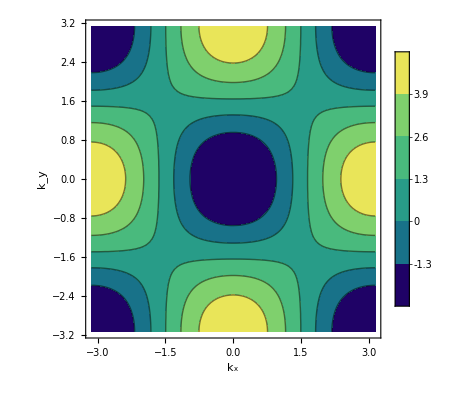
Basis:  | (1. | 1.
-1. | 1.)
Hopping:  | {-1.}
Dispersion:  | 1.-2. Cos[1. k_x-1. k_y]-2. Cos[1. k_x+1. k_y]
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 1.}, {-1., 1.}};
orbitalEnergy = 1.;
hop = {-1.};
band := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop |>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

```mathematica
orbitalEnergy = 1.;
hop = {-1.};
bandM[basis_] := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop |>];
InfoGrid[basis_] := Grid[{{"Basis: ", basis // MatrixForm},
  			{"Hopping: ", hop},
  			{"Dispersion: ", bandM[basis]},
  {
   PlotDispersion2DContour[bandM[basis]],
   PlotDispersion2D[bandM[basis]]
   }}]

Manipulate[InfoGrid[{a, b}], 
Row[{Control[{{a, {1, 0}}, {0, 0}, {1, 1}}], 
	Control[{{b, {0, 1}}, {-1, -1}, {1, 1}}]}]]
```

More Hopping

## Let' s add next-nearest hopping

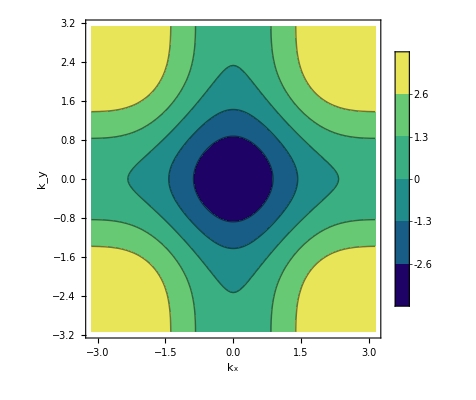
Basis:  | (1. | 0
0 | 1.)
Hopping:  | {-1.,-0.2}
Dispersion:  | 1.-2. Cos[0.+1. k_x]-0.4 Cos[2 (0.+1. k_x)]-2. Cos[0.+1. k_y]-0.4 Cos[2 (0.+1. k_y)]
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 0}, {0, 1.}};
orbitalEnergy = 1.;
hop = {-1., -.2};
band := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop |>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

## Let' s add next-next-nearest hopping

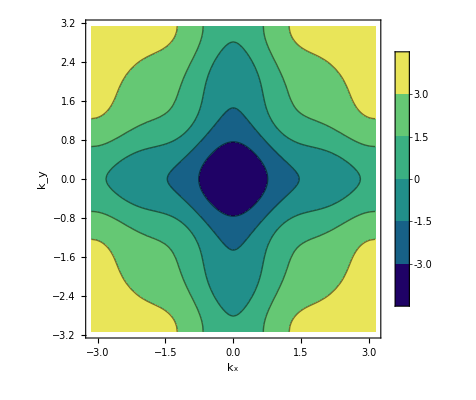
Basis:  | (1. | 0
0 | 1.)
Hopping:  | {-1.,-0.2,-0.2}
Dispersion:  | 1.-2. Cos[0.+1. k_x]-0.4 Cos[2 (0.+1. k_x)]-0.4 Cos[3 (0.+1. k_x)]-2. Cos[0.+1. k_y]-0.4 Cos[2 (0.+1. k_y)]-0.4 Cos[3 (0.+1. k_y)]
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 0}, {0, 1.}};
orbitalEnergy = 1.;
hop = {-1., -.2, -.2};
band := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop |>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

Let' s add diagonal hopping

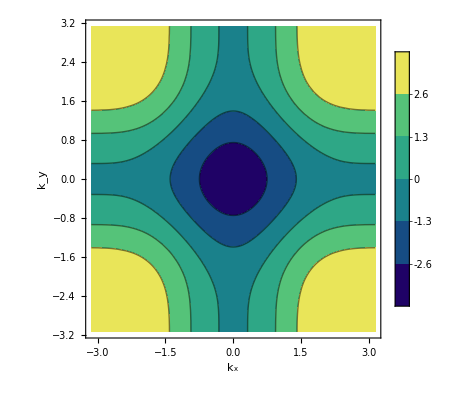
Basis:  | (1. | 0
0 | 1.)
Hopping:  | {-1.,-0.2}
Diagonal Hopping:  | {0.1}
Dispersion:  | 1.-2. Cos[0.+1. k_x]-0.4 Cos[2 (0.+1. k_x)]+0.2 Cos[1. k_x-1. k_y]-2. Cos[0.+1. k_y]-0.4 Cos[2 (0.+1. k_y)]+0.2 Cos[1. k_x+1. k_y]
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 0}, {0, 1.}};
orbitalEnergy = 1.;
hop = {-1., -.2};
diag = {.1};
band := Cosine2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop, 11 -> diag, {1,-1} -> diag|>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Diagonal Hopping: ", diag},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

What about overlap?

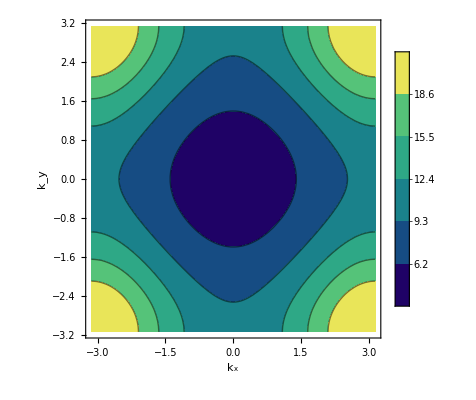
Basis:  | (1. | 0
0 | 1.)
Hopping:  | {-1.}
Overlap:  | {0.1}
Dispersion:  | (10.-2. Cos[0.+1. k_x]-2. Cos[0.+1. k_y])/(1+0.2 Cos[0.+1. k_x]+0.2 Cos[0.+1. k_y])
-Graphics- | -Graphics3D-

```mathematica
basis = {{1., 0}, {0, 1.}};
orbitalEnergy = 10.;
hop = {-1.};
overlap = {.1};
band := Full2D[orbitalEnergy, basis,
				<| 10 -> hop, 01 -> hop |>,
				<| 10 -> overlap, 01 -> overlap |>];
Grid[{{"Basis: ", basis // MatrixForm},
  	{"Hopping: ", hop},
  	{"Overlap: ", overlap},
  	{"Dispersion: ", band},
  {
   PlotDispersion2DContour[band],
   PlotDispersion2D[band]
   }}]
```

Putting it all together

```mathematica
orbitalEnergy = 1.;
band3[basis_, hop_, diag_, overlap_] := Full2D[orbitalEnergy, basis, <| 10 -> hop, 01 -> hop,
																	11 -> diag, {1, -1} -> diag |>,
																<| 10 -> overlap, 01 -> overlap |>];
InfoGrid2[basis_, hop_, diag_, overlap_] := With[
	{disp = band3[basis, hop, diag, overlap]},
	Grid[{{"Basis: ", basis // MatrixForm},
  			{"Hopping: ", hop},
  			{"Diagonal Hop: ", diag},
  			{"Overlap: ", overlap},
  			{"Dispersion: ", disp},
  {
   PlotDispersion2DContour[disp],
   PlotDispersion2D[disp]
   }}]]

Manipulate[InfoGrid2[Transpose @ {a, b}, {t1, t2}, {d}, {o}], 
Grid[{
{Control @ {{a, {1, 0}}, {0, 0}, {1, 1}}, 
 Control @ {{b, {0, 1}}, {-1, -1}, {1, 1}}},
{Control @ {t1, 0, -2}, Control @ {{d, 0}, -1, 1}},
{Control @ {{t2, 0}, -1, 1},Control @ {{o, 0}, 0, 1}}
}]]
```

## Extension to Multiple bands

Dispersion relation is given the generalized Eigenvalue problem det(η - Eσ) = 0, where η_ijare objects like the simple dispersion relations above, but generalized to hopping between orbitals, σ is an analogous matrix for the overlap.

Let's try a s & p_z at a single atomic site, meaning no overlap between them and higher s hopping to the neighbouring unit cell

```mathematica
basis = Transpose @ {{1, 0}, {0, 1}};
band4[basis_, e0_, hop_, diag_] := Cosine2D[e0, basis, <| 10 -> hop, 01 -> hop,
														    11 -> diag, {1, -1} -> diag |>];
bandH = {{band4[basis, 2, {-1}, {}], 0},
	{0, band4[basis, 10, {-.2}, {}]}};
PlotDispersion2D[Eigenvalues[bandH]]
```

-Graphics3D-

Let's try two orbits at a single atomic site, with some overlap and in a similar energy range

```mathematica
basis = Transpose @ {{1, 0}, {0, 1}};
band4[basis_, e0_, hop_, diag_] := Cosine2D[e0, basis, <| 10 -> hop, 01 -> hop,
														    11 -> diag, {1, -1} -> diag |>];
bandHnon = {{band4[basis, 0, {-1}, {}], 0},
	{0, band4[basis, 0, {-.2}, {}]}};
bandH = {{band4[basis, 0, {-1}, {}], -1.1},
	   {-1.1, band4[basis, 0, {-.2}, {}]}};
Row[{
PlotDispersion2D[Eigenvalues[bandHnon], Title -> "No overlap"],
PlotDispersion2D[Eigenvalues[bandH], Title -> "Hybridization Gap!"]
}]
```

-Graphics3D--Graphics3D-

Square unit cell, two orbitals per unit cell, no overlap, hopping only within unit cell

```mathematica
basis = Transpose @ {{1, 0}, {0, 1}};
band4[basis_, e0_, hop_, diag_] := Cosine2D[e0, basis, <| 10 -> hop, 01 -> hop,
														    11 -> diag, {1, -1} -> diag |>];
bandH = {{0, band4[basis, 1, {-.2}, {}]},
	{band4[basis, 1, {-.2}, {}], 0}};
bands1s1p = Eigenvalues[bandH];
PlotDispersion2D[bands1s1p]
```

-Graphics3D-

Square unit cell, 1 p_x & 1 p_y per unit cell, no overlap

```mathematica
basis = Transpose @ {{1, 0}, {0, 1}};
band4[basis_, e0_, hop_, diag_] := Cosine2D[e0, basis, <| 10 -> hop, 01 -> hop,
														    11 -> diag, {1, -1} -> diag |>];
bandH = {{Cosine2D[10, basis, <| 10 ->{-1} |>], .2},
	{.2, Cosine2D[10, basis, <| 01 ->{-1} |>]}};
PlotDispersion2D[Eigenvalues[bandH]]
```

-Graphics3D-

Square unit cell, 1 p_x & 1 p_y per unit cell (you have to squint)

```mathematica
basis = Transpose @ {{1, 0}, {0, 1}};
band4[basis_, e0_, hop_, diag_] := Cosine2D[e0, basis, <| 10 -> hop, 01 -> hop,
														    11 -> diag, {1, -1} -> diag |>];
bandH = {{Cosine2D[10, basis, <| 10 ->{-1} |>], .2},
	{.2, Cosine2D[10, basis, <| 01 ->{-1} |>]}};
bandS = {{1, .02},
	    {.02, 1}};
PlotDispersion2D[Eigenvalues[{bandH,bandS}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

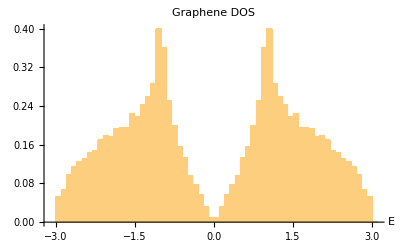

```mathematica
Sq[λ_] := If[ λ > 0, Sqrt[λ], -Sqrt[-λ]];
DOS2D[Disp_, n_ : 1000] := Histogram[Sq /@ Flatten @ Table[Disp,
						{Subscript[k, x], -π, π, 2π/n}, {Subscript[k, y], -π, π, 2π/n}], 50, "PDF",
PlotLabel -> "Graphene DOS", AxesLabel -> {"E"}];
DOS2D[grapheneBands1, 100]
```

Last try, planar dioxides e.g. CuO_2, i.e. three atoms with one orbitals per unit cell

```mathematica
basis =Transpose @ {{1, 0}, {0, 1}};
bandH = {{-Cu, -Cosine2D[CuO, basis , <| 01 -> {CuO} |>], -Cosine2D[CuO, basis , <| 10 -> {CuO} |>]},
	    {-Cosine2D[CuO, basis , <| 01 -> {CuO} |>], -O, 0},
	    {-Cosine2D[CuO, basis , <| 10 -> {CuO} |>], 0,-O}};
bandH // MatrixForm
grapheneBands1 = Eigenvalues[bandH];
PlotDispersion2D[ grapheneBands1 /. {CuO -> 1.2, Cu -> 0, O -> 3.6}] (* the values here are from a paper Thomas showed me, but I forgot which one. :/ *)
```

(-Cu | -CuO-2 CuO Cos[k_y] | -CuO-2 CuO Cos[k_x]
-CuO-2 CuO Cos[k_y] | -O | 0
-CuO-2 CuO Cos[k_x] | 0 | -O)

-Graphics3D-